## Setting everything up

```mathematica
logSpace[start_,end_,num_]:=10^(Range[Log10[start],Log10[end],(Log10[end]-Log10[start])/(num-1)])
Mpc=3.086*10^24 (*cm in 1 Mpc*);
(*Ωm=0.315;
ΩΛ=0.685;*)
Ωm=0.3;
ΩΛ=0.7;
c=299792.458  km*s^-1;
H0=67.36 km*s^-1;
dH=c/H0 (*Mpc*);
e[z_]:=Sqrt[Ωm*(1+z)^3+ΩΛ]
dΩ=4*Pi;
(*dC[z_]:=dH*Integrate[1/e[z2],{z2,0,z}];*)
dC[z_?NumericQ]:=dH*(-1.140667+1.195229 (1+z) Hypergeometric2F1[1/3,1/2,4/3,-Ωm/ΩΛ*(1+z)^3])(*Analytic solution to the above integral*)
dA[z_]:=dC[z]/(1+z)
dL[z_?NumericQ]:=dA[z]*(1+z)^2
dVdz[z_?NumericQ]:=dH*((1+z)^2*dA[z]^2)/e[z]*dΩ(*Mpc^3, agrees with cosmolopy, note that cosmolopy gives dVdz/dΩ*)
```

## Qu

## Stuff needed for reproductions

### Digitizations

```mathematica
AppendTo[$Path, "/Users/matias/Downloads/"];
dNdzPLEqu=Import["blazar_data/old_digitizations/dNdz_ple_qu.csv"] (* from fig. 3 of 1909.07542 (Qu) *);
dNdzPDEqu=Import["blazar_data/old_digitizations/dNdz_pde_qu.csv"];
dNdzLDDEqu=Import["blazar_data/old_digitizations/dNdz_ldde_qu.csv"];
dNdΓPLEquOld=Import["blazar_data/old_digitizations/dNdG_ple_qu.csv"] ;
dNdΓPLEqu=Delete[dNdΓPLEquOld,101];
dNdΓPDEqu=Import["blazar_data/old_digitizations/dNdG_pde_qu.csv"];
dNdΓLDDEqu=Import["blazar_data/old_digitizations/dNdG_ldde_qu.csv"];
dNdlPLEqu=Import["blazar_data/old_digitizations/dNdl_ple_qu.csv"] ;
dNdlPDEqu=Import["blazar_data/old_digitizations/dNdl_pde_qu.csv"] ;
dNdlLDDEqu=Import["blazar_data/old_digitizations/dNdl_ldde_qu.csv"];
botRightFigQu=Import["blazar_data/old_digitizations/botRightFigQu.csv","CSV"];
fermiSensitivityQu= Import["fermiSensitivityQu.csv","CSV"];
fermiSensitivityFuncOldQu=Interpolation[fermiSensitivityQu,InterpolationOrder->1];
fermiSensitivityFuncQu[x_]:=Module[{val},
If[x<2*10^-10,0,
val =Evaluate[fermiSensitivityFuncOldQu][x];
If[x>10^-8||val>1,1,
val]
]
]
```

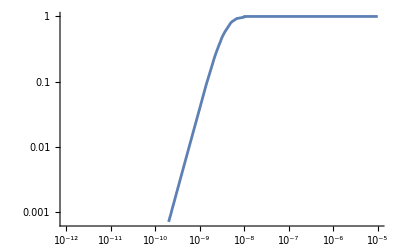

```mathematica
LogLogPlot[fermiSensitivityFuncQu[x],{x,10^-12,10^-5}]
```

### Luminosity functions

```mathematica
ΦPLEqu[Lext_,Γext_,zext_]:=Module[{A=10^-6.39,γ1=0.62,γ2=1.92,Lstar=10^44.72,kstar=4.23,τ=0.7,ξ=-0.43,μstar=1.93,β=0.066,σ=0.23,μ,kd,evo,Φ0},
μ[L_]:=μstar+β*(Log10[L]-46);
kd[L_]:=kstar+τ*(Log10[L]-46);
evo[L_,z_]:=(1+z)^kd[L]*Exp[z/ξ];
Φ0[L_,Γ_]:=A/(Log[10]*L)*((L/Lstar)^γ1+(L/Lstar)^γ2)^-1*Exp[(-0.5*(Γ-μ[L])^2)/σ^2];
Φ0[Lext/evo[Lext,zext],Γext]
](*Mpc^-3*);

ΦPDEqu[Lext_,Γext_,zext_]:=Module[{A=10^-6.41,γ1=1.89,γ2=0.72,Lstar=10^44.69,kstar=13.53,τ=1.97,ξ=-0.13,μstar=1.93,β=0.08,σ=0.23,μ,kd,evo,Φ0},
μ[L_]:=μstar+β*(Log10[L]-46);
kd[L_]:=kstar+τ*(Log10[L]-46);
evo[L_,z_]:=(1+z)^kd[L]*Exp[z/ξ];
Φ0[L_,Γ_]:=A/(Log[10]*L)*((L/Lstar)^γ1+(L/Lstar)^γ2)^-1*Exp[(-0.5*(Γ-μ[L])^2)/σ^2];
Φ0[Lext,Γext]*evo[Lext,zext]
] (*Mpc^-3*);

ΦLDDEqu[Lext_,Γext_,zext_]:=Module[{A=10^-5.32,γ1=1.37,γ2=0.51,Lstar=10^44.28,kstar=4.81,τ=-1.6,p2=-8.27,zcstar=0.94,α=0.14,μstar=1.93,β=0.083,σ=0.23,μ,zc,p1,evo,Φ0},
μ[L_]:=μstar+β*(Log10[L]-46);
zc[L_]:=zcstar*(L/10^48)^α;
p1[L_]:=kstar+τ*(Log10[L]-46);
evo[L_,z_]:=(((1+z)/(1+zc[L]))^p1[L]+((1+z)/(1+zc[L]))^p2)^-1;
Φ0[L_,Γ_]:=A/(Log[10]*L)*((L/Lstar)^γ1+(L/Lstar)^γ2)^-1*Exp[(-0.5*(Γ-μ[L])^2)/σ^2];
Φ0[Lext,Γext]*evo[Lext,zext]
](*Mpc^-3, note that this one might not work since they do not give δ in their paper*);
```

### Flux

```mathematica
fluxQu[L_?NumericQ,Γ_?NumericQ,z_?NumericQ,EminGeV_,EmaxGeV_]:=Module[{h=6.62607015*^-27,(*erg s*)nuFactor=2.418*^23,(*Hz/GeV*)α,ν1,ν2,Sγ,Fγ,dLcm},
α=Γ-1;
ν1=EminGeV*nuFactor;
ν2=EmaxGeV*nuFactor;
dLcm=dL[z]*Mpc;
Sγ=L*(1+z)^(1-α)/(4 Pi*dLcm^2);If[α!=1,Fγ=(Sγ*(1-α))/(α*h*ν1*((ν2/ν1)^(1-α)-1)),Fγ=Sγ/(h*ν1*Log[ν2/ν1])];
Fγ]
```

## Reproductions

### dNdz

```mathematica
dNdzPLEfuncQu[z_]:=dVdz[z]*NIntegrate[Exp[L]*ΦPLEqu[Exp[L],Γ,z]*fermiSensitivityFuncQu[fluxQu[Exp[L],Γ,z,0.1,100]],{Γ,1.4,3},{L,Log[4*10^40],Log[10^50]},PrecisionGoal->3,Method->{"QuasiMonteCarlo"}]//Quiet
dNdzPDEfuncQu[z_]:=dVdz[z]*NIntegrate[Exp[L]*ΦPDEqu[Exp[L],Γ,z]*fermiSensitivityFuncQu[fluxQu[Exp[L],Γ,z,0.1,100]],{Γ,1.4,3},{L,Log[4*10^40],Log[10^50]},Method->{"QuasiMonteCarlo"},PrecisionGoal->3,Method->{Automatic,"SymbolicProcessing"->0}]//Quiet
dNdzLDDEfuncQu[z_]:=dVdz[z]*NIntegrate[Exp[L]*ΦLDDEqu[Exp[L],Γ,z]*fermiSensitivityFuncQu[fluxQu[Exp[L],Γ,z,0.1,100]],{Γ,1.4,3},{L,Log[4*10^40],Log[10^50]},Method->{"QuasiMonteCarlo"}]
```

```mathematica
dNdzLDDEfuncQu[1]
```

97.5919

```mathematica
zArr=logSpace[10^-3,2.58,16];
(*dNdzPLEarrQu=ParallelTable[{z,dNdzPLEfuncQu[z]},{z,zArr}];
CloseKernels[];
LaunchKernels[];
dNdzPDEarrQu=ParallelTable[{z,dNdzPDEfuncQu[z]},{z,zArr}];
CloseKernels[];
LaunchKernels[];*)
dNdzLDDEarrQu=ParallelTable[{z,dNdzLDDEfuncQu[z]},{z,zArr}];
CloseKernels[];
LaunchKernels[];
```

NIntegrate::maxp: The integral failed to converge after 50000 integrand evaluations. NIntegrate obtained 6.54288×10^-9 and 1.17011×10^-10 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 50000 integrand evaluations. NIntegrate obtained 1.18752×10^-10 and 1.95089×10^-12 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 50000 integrand evaluations. NIntegrate obtained 3.83557×10^-7 and 6.82239×10^-9 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 50000 integrand evaluations. NIntegrate obtained 6.93339×10^-8 and 1.26525×10^-9 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 50000 integrand evaluations. NIntegrate obtained 1.71478×10^-6 and 2.87107×10^-8 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 50000 integrand evaluations. NIntegrate obtained 0.0000207733 and 3.33111×10^-7 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 50000 integrand evaluations. NIntegrate obtained 6.41846×10^-6 and 1.02691×10^-7 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 50000 integrand evaluations. NIntegrate obtained 0.0000438238 and 8.56172×10^-7 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 50000 integrand evaluations. NIntegrate obtained 1.67688×10^-11 and 2.64831×10^-13 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 50000 integrand evaluations. NIntegrate obtained 9.95211×10^-10 and 1.70756×10^-11 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 50000 integrand evaluations. NIntegrate obtained 2.53759×10^-8 and 4.61157×10^-10 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 50000 integrand evaluations. NIntegrate obtained 1.67832×10^-7 and 3.04486×10^-9 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 50000 integrand evaluations. NIntegrate obtained 8.31688×10^-7 and 1.43658×10^-8 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 50000 integrand evaluations. NIntegrate obtained 3.38133×10^-6 and 5.51235×10^-8 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 50000 integrand evaluations. NIntegrate obtained 0.0000117794 and 1.8682×10^-7 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 50000 integrand evaluations. NIntegrate obtained 0.0000335005 and 5.7599×10^-7 for the integral and error estimates.

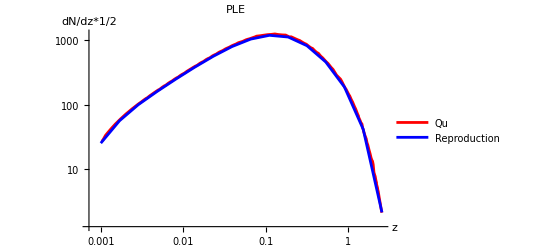

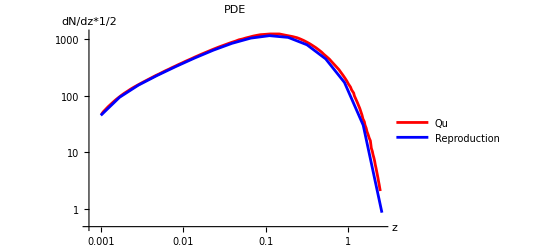

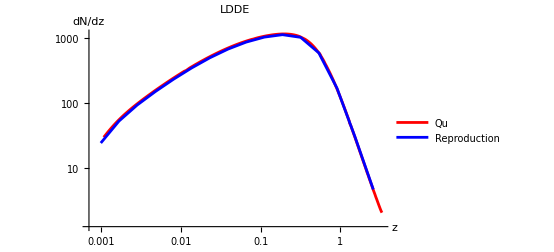

```mathematica
ListLogLogPlot[{dNdzPLEqu,Transpose[{dNdzPLEarrQu[[All,1]],dNdzPLEarrQu[[All,2]]*1/2}]},Joined->True,PlotStyle->{Red,Blue},PlotLabel->"PLE",AxesLabel->{"z","dN/dz*1/2 "},PlotLegends->Placed[{ "Qu","Reproduction"},{0.65,0.2}]]
ListLogLogPlot[{dNdzPDEqu,Transpose[{dNdzPDEarrQu[[All,1]],dNdzPDEarrQu[[All,2]]*1/2}]},Joined->True,PlotStyle->{Red,Blue},PlotLabel->"PDE",AxesLabel->{"z","dN/dz*1/2 "},PlotLegends->Placed[{ "Qu","Reproduction"},{0.65,0.2}]]
ListLogLogPlot[{dNdzLDDEqu,Transpose[{dNdzLDDEarrQu[[All,1]],dNdzLDDEarrQu[[All,2]]/2}]},Joined->True,PlotStyle->{Red,Blue},PlotLabel->"LDDE",AxesLabel->{"z","dN/dz"},PlotLegends->Placed[{ "Qu","Reproduction"},{0.65,0.2}]]
```

### dNdΓ

```mathematica
dNdΓPLEfuncQu[Γ_]:=NIntegrate[Exp[L]*dVdz[z]*ΦPLEqu[Exp[L],Γ,z]*fermiSensitivityFuncQu[fluxQu[Exp[L],Γ,z,0.1,100]],{z,0,6},{L,Log[4*10^40],Log[10^50]},PrecisionGoal->6,Method->{Automatic,"SymbolicProcessing"->0}]//Quiet
dNdΓPDEfuncQu[Γ_]:=NIntegrate[Exp[L]*dVdz[z]*ΦPDEqu[Exp[L],Γ,z]*fermiSensitivityFuncQu[fluxQu[Exp[L],Γ,z,0.1,100]],{z,0,6},{L,Log[4*10^40],Log[10^50]},PrecisionGoal->6,Method->{Automatic,"SymbolicProcessing"->0}]//Quiet
```

```mathematica
Γarr=Range[1+.1,3,2/16];
dNdΓPLEarrQu=ParallelTable[{Γ,dNdΓPLEfuncQu[Γ]},{Γ,Γarr}];
CloseKernels[];
LaunchKernels[];
dNdΓPDEarrQu=ParallelTable[{Γ,dNdΓPDEfuncQu[Γ]},{Γ,Γarr}];
CloseKernels[];
LaunchKernels[];
```

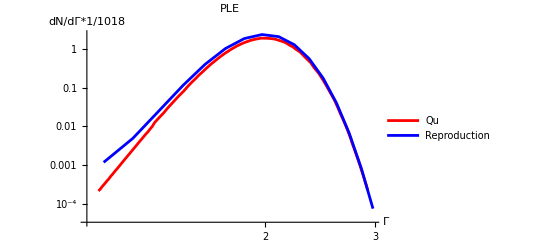

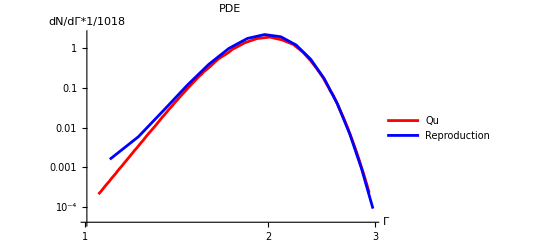

```mathematica
Nexp=1018 (*Number of expected sources. I'm not sure if it should be 1018 or 649. 1018 looks better, but it would make sense that it is actually 649 and just off by a factor of 2 like the dNdz figure*);
ListLogLogPlot[{dNdΓPLEqu,Transpose[{dNdΓPLEarrQu[[All,1]],dNdΓPLEarrQu[[All,2]]/Nexp}]},Joined->True,PlotStyle->{Red,Blue},PlotLabel->"PLE",AxesLabel->{"Γ","dN/dΓ*1/1018"},
PlotLegends->Placed[{ "Qu","Reproduction"},{0.65,0.2}]]
ListLogLogPlot[{dNdΓPDEqu,Transpose[{dNdΓPDEarrQu[[All,1]],dNdΓPDEarrQu[[All,2]]/Nexp}]},Joined->True,PlotStyle->{Red,Blue},PlotLabel->"PDE",AxesLabel->{"Γ","dN/dΓ*1/1018"},
PlotLegends->Placed[{ "Qu","Reproduction"},{0.65,0.2}]]
```

### dNdL

```mathematica
dNdLpleQu[L_]:=NIntegrate[dVdz[z]*ΦPLEqu[L,Γ,z]*fermiSensitivityFuncQu[fluxQu[L,Γ,z,0.1,100]],{z,0,6},{Γ,1.4,3},PrecisionGoal->5,MinRecursion->10,MaxRecursion->20,WorkingPrecision->6,Method->{Automatic}]//Quiet
dNdLpdeQu[L_]:=NIntegrate[dVdz[z]*ΦPDEqu[L,Γ,z]*fermiSensitivityFuncQu[fluxQu[L,Γ,z,0.1,100]],{z,0,6},{Γ,1.4,3},PrecisionGoal->3,MinRecursion->8,WorkingPrecision->6,Method->{Automatic}]//Quiet
```

```mathematica
Larr=logSpace[2.6*^40,4.2*^48,16];
dNdLResultPLEqu=ParallelTable[{L,dNdLpleQu[L]},{L,Larr}];
CloseKernels[];
LaunchKernels[];
(*dNdLResultPDEqu=ParallelTable[{L,dNdLpdeQu[L]},{L,Larr}];
CloseKernels[];
LaunchKernels[];*)
```

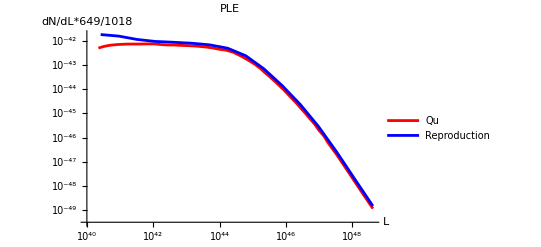

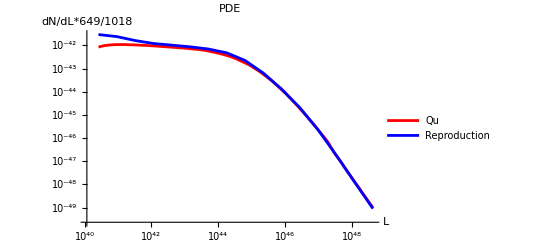

```mathematica
ListLogLogPlot[{dNdlPLEqu,Transpose[{dNdLResultPLEqu[[All,1]],dNdLResultPLEqu[[All,2]]*649/1018}]},Joined->True,PlotStyle->{Red,Blue},PlotLabel->"PLE",AxesLabel->{"L","dN/dL*649/1018"},
PlotLegends->Placed[{ "Qu","Reproduction"},{0.65,0.2}]]
ListLogLogPlot[{dNdlPDEqu,Transpose[{dNdLResultPDEqu[[All,1]],dNdLResultPDEqu[[All,2]]*649/1018}]},Joined->True,PlotStyle->{Red,Blue},PlotLabel->"PDE",AxesLabel->{"L","dN/dL*649/1018"},
PlotLegends->Placed[{ "Qu","Reproduction"},{0.65,0.2}]]
```

### Bottom right figure

```mathematica
LminQu[F_?NumericQ,Γ_?NumericQ,z_?NumericQ,EminGeV_,EmaxGeV_]:=Module[
{h=6.62607015*^-27,nuFactor=2.418*^23,α,ν1,ν2,dLcm},
α=Γ-1;
ν1=EminGeV*nuFactor;
ν2=EmaxGeV*nuFactor;
dLcm=dL[z]*Mpc;
If[α!=1,F*(4*Pi*dLcm^2)/(1+z)^(1-α)*((α*h*ν1*((ν2/ν1)^(1-α)-1))/(1-α)),
F*4*Pi*dLcm^2*h*ν1*Log[ν2/ν1]]]
```

```mathematica
botRightIntPLEqu[fluxmin_]:=Pi/(4*180^2)*NIntegrate[Exp[L]*dVdz[z]*ΦPLEqu[Exp[L],Γ,z]*fermiSensitivityFuncQu[fluxQu[Exp[L],Γ,z,0.1,100]],{Γ,1.4,3},{z,0,6},{L,Log[LminQu[fluxmin,Γ,z,0.1,100]],Log[10^50]},PrecisionGoal->3]//Quiet
botRightIntPDEqu[fluxmin_]:=Pi/(4*180^2)*NIntegrate[Exp[L]*dVdz[z]*ΦPDEqu[Exp[L],Γ,z]*fermiSensitivityFuncQu[fluxQu[Exp[L],Γ,z,0.1,100]],{Γ,1.4,3},{z,0,6},{L,Log[LminQu[fluxmin,Γ,z,0.1,100]],Log[10^50]},PrecisionGoal->3]//Quiet
```

```mathematica
Farr=logSpace[10^-10,10^-6,16];
botRightResultPLEqu=ParallelTable[{F,botRightIntPLEqu[F]},{F,Farr}];
CloseKernels[];
LaunchKernels[];
botRightResultPDEqu=ParallelTable[{F,botRightIntPDEqu[F]},{F,Farr}];
CloseKernels[];
LaunchKernels[];
```

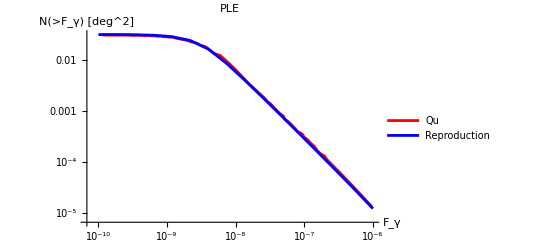

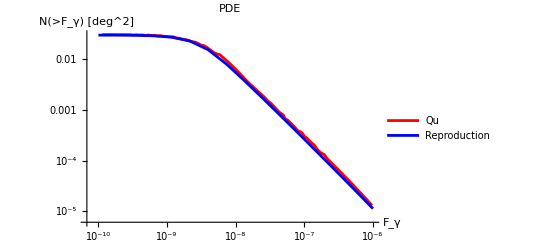

```mathematica
ListLogLogPlot[{botRightFigQu,botRightResultPLEqu},Joined->True,PlotStyle->{Red,Blue},PlotLabel->"PLE",AxesLabel->{"F_γ","N(>F_γ) [deg^2]"},
PlotLegends->Placed[{ "Qu","Reproduction"},{0.65,0.2}]]
ListLogLogPlot[{botRightFigQu,botRightResultPDEqu},Joined->True,PlotStyle->{Red,Blue},PlotLabel->"PDE",AxesLabel->{"F_γ","N(>F_γ) [deg^2]"},
PlotLegends->Placed[{ "Qu","Reproduction"},{0.65,0.2}]]
```

```mathematica
dNdzPLEfuncQu[z_]:=NIntegrate[Exp[L]*ΦPLEqu[Exp[L],Γ,z],{Γ,1.4,3},{L,Log[4*10^40],Log[10^50]},PrecisionGoal->3,Method->{Automatic,"SymbolicProcessing"->0}]//Quiet
dNdzPDEfuncQu[z_]:=NIntegrate[Exp[L]*ΦPDEqu[Exp[L],Γ,z],{Γ,1.4,3},{L,Log[4*10^40],Log[10^50]},PrecisionGoal->3,Method->{Automatic,"SymbolicProcessing"->0}]//Quiet
```

```mathematica
zArr=Range[0,3,3/16];
dNdzPLEarrQu=ParallelTable[{z,dNdzPLEfuncQu[z]},{z,zArr}];
CloseKernels[];
LaunchKernels[];
dNdzPDEarrQu=ParallelTable[{z,dNdzPDEfuncQu[z]},{z,zArr}];
CloseKernels[];
LaunchKernels[];
```

```mathematica
belowFig= Import["Qu_fig4_left.csv","CSV"];
```

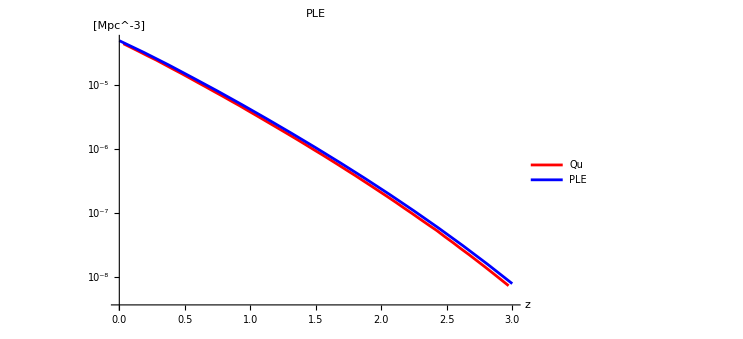

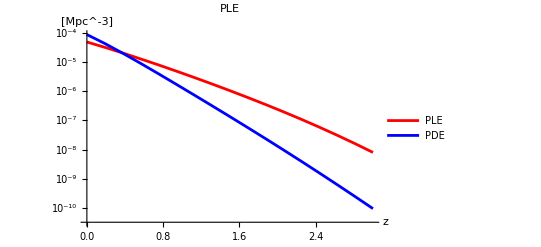

```mathematica
ListLogPlot[{belowFig, Transpose[{dNdzPLEarrQu[[All,1]],dNdzPLEarrQu[[All,2]]}]},Joined->True,PlotStyle->{Red,Blue},PlotLabel->"PLE",AxesLabel->{"z","[Mpc^-3]"},PlotLegends->Placed[{ "Qu","PLE"},{0.65,0.2}]]
ListLogPlot[{Transpose[{dNdzPLEarrQu[[All,1]],dNdzPLEarrQu[[All,2]]}],Transpose[{dNdzPDEarrQu[[All,1]],dNdzPDEarrQu[[All,2]]}]},Joined->True,PlotStyle->{Red,Blue},PlotLabel->"PLE",AxesLabel->{"z","[Mpc^-3]"},PlotLegends->Placed[{ "PLE","PDE"},{0.65,0.2}]]
```

## Ajello

## Stuff needed for reproductions

### Digitizations

```mathematica
dNdΓAjello= Import["blazar_data/old_digitizations/topRightFig.csv","CSV"]; (* from fig. 1 of 1501.05301 *)
botLeftFig= Import["blazar_data/old_digitizations/botLeftFig.csv","CSV"];
botRightFig= Import["blazar_data/old_digitizations/botRightFig.csv","CSV"];
botRightFigUpper= Import["blazar_data/old_digitizations/botRightFigUpper.csv","CSV"];
botRightFigLower= Import["blazar_data/old_digitizations/botRightFigLower.csv","CSV"];
dNdzAjello= Import["blazar_data/old_digitizations/topLeftFig.csv","CSV"];
dNdLajello = Import["blazar_data/old_digitizations/dNdL.csv"] (* from Ajello talk *);
fermiSensitivityAjello= Import["blazar_data/fermiDetectionSensitivity.csv","CSV"]; (* from fig. 7 of 1003.0895 *)
```

```mathematica
fermiSensitivityFuncOldAjello=Interpolation[fermiSensitivityAjello,InterpolationOrder->1];
fermiSensitivityFuncAjello[x_]:=Module[{value},
If[x<2.1*^-10,0,
value=Evaluate[fermiSensitivityFuncOldAjello][x];
If[x>10^-6||value>1,1,value]]
]
```

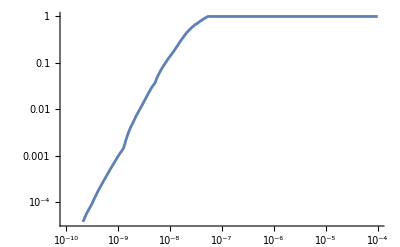

```mathematica
LogLogPlot[fermiSensitivityFuncAjello[x],{x,10^-10,10^-4}]
```

### Luminosity functions

```mathematica
ΦPLEajello[Lext_,Γext_,zext_]:=Module[{A=.193*10^-9,γ1=3.19,γ2=1.14,Lstar=8.75*^46,kstar=4.41,τ=0.91,ξ=-0.43,μstar=2.22,β=0.1,σ=0.28,μ,kd,evo,Φ0},
μ[L_]:=μstar+β*(Log10[L]-46);
kd[L_]:=kstar+τ*(Log10[L]-46);
evo[L_,z_]:=(1+z)^kd[L]*Exp[z/ξ];
Φ0[L_,Γ_]:=A/(Log[10]*L)*((L/Lstar)^γ1+(L/Lstar)^γ2)^-1*Exp[(-0.5*(Γ-μ[L])^2)/σ^2];
Φ0[Lext/evo[Lext,zext],Γext]
](*Mpc^-3*);


ΦPDEajello[Lext_,Γext_,zext_]:=Module[{A=0.0122*^-9,γ1=2.8,γ2=1.26,Lstar=0.44*^48,kstar=12.14,τ=2.79,ξ=-0.15,μstar=2.22,β=0.1,σ=0.28,μ,kd,evo,Φ0},
μ[L_]:=μstar+β*(Log10[L]-46);
kd[L_]:=kstar+τ*(Log10[L]-46);
evo[L_,z_]:=(1+z)^kd[L]*Exp[z/ξ];
Φ0[L_,Γ_]:=A/(Log[10]*L)*((L/Lstar)^γ1+(L/Lstar)^γ2)^-1*Exp[(-0.5*(Γ-μ[L])^2)/σ^2];
Φ0[Lext,Γext]*evo[Lext,zext]
] (*Mpc^-3*);

ΦLDDEajello[Lext_,Γext_,zext_]:=Module[{A=1.96*^-9,γ1=0.5,γ2=1.83,Lstar=1.05*^48,kstar=3.39,τ=3.16,ξ=-4.96,zcstar=1.25,δ=0.64 ,α=0.0723,μstar=2.22,β=0.1,σ=0.28,μ,zc,p1,p2,evo,Φ0},
μ[L_]:=μstar+β*(Log10[L]-46);
zc[L_]:=zcstar*(L/10^48)^α;
p1[L_]:=kstar+τ*(Log10[L]-46);
p2[L_]:=ξ+δ*(Log10[L]-46);
evo[L_,z_]:=(((1+z)/(1+zc[L]))^(-p1[L])+((1+z)/(1+zc[L]))^(-p2[L]))^-1;
Φ0[L_,Γ_]:=A/(Log[10]*L)*((L/Lstar)^γ1+(L/Lstar)^γ2)^-1*Exp[(-0.5*(Γ-μ[L])^2)/σ^2];
Φ0[Lext,Γext]*evo[Lext,zext]
](*Mpc^-3*);
```

### Flux

#### Optical depth

```mathematica
redshift002Arr= Import["blazar_data/finkeEBL/redshift002.csv","CSV"]; (* digitized from fig 6 of 2210.01157 *)
redshift05Arr= Import["blazar_data/finkeEBL/redshift05.csv","CSV"];  (* digitized from fig. 9 of APJ 712:238–249 *)
redshift1Arr= Import["blazar_data/finkeEBL/redshift1.csv","CSV"]; 
redshift2Arr= Import["blazar_data/finkeEBL/redshift2.csv","CSV"]; 
redshift3Arr= Import["blazar_data/finkeEBL/redshift3.csv","CSV"]; 
redshift002Arr[[All,1]]=#*1000&/@redshift002Arr[[All,1]]; (* converts TeV to GeV *)
redshift05Arr[[All,1]]=#*1000&/@redshift05Arr[[All,1]]; 
redshift1Arr[[All,1]]=#*1000&/@redshift1Arr[[All,1]];
redshift2Arr[[All,1]]=#*1000&/@redshift2Arr[[All,1]];
redshift3Arr[[All,1]]=#*1000&/@redshift3Arr[[All,1]];
redshift002=Interpolation[redshift002Arr,InterpolationOrder->1];
redshift05=Interpolation[redshift05Arr,InterpolationOrder->1];
redshift1=Interpolation[redshift1Arr,InterpolationOrder->1];
redshift2=Interpolation[redshift2Arr,InterpolationOrder->1];
redshift3=Interpolation[redshift3Arr,InterpolationOrder->1];
levelsets={{0.02,redshift002},{0.5,redshift05},{1,redshift1},{2,redshift2},{3,redshift3}};
energyValues=logSpace[Min[redshift05Arr[[All,1]]],Max[redshift05Arr[[All,1]]],100];
examplePoints=Flatten[Table[
With[
{z=levelsets[[i]][[1]],f=levelsets[[i]][[2]]},Table[{energyValues[[j]],z,f[energyValues[[j]]]},{j,Length[energyValues]}]
],
{i,Length[levelsets]}],1];
opticalDepth=Interpolation[examplePoints,InterpolationOrder->1] (* function of Energy and z *);
expOpticalDepth[En_?NumericQ,z_?NumericQ]:=Module[{value,zValue},
zValue=Max[z,0.02];
value=Exp[-Evaluate[opticalDepth][En,zValue]];
If[value<1,value,1]
] (* since expOpticalDepth doesn't greatly change at low redshifts I can just take z=0.02 (lowest redshift I have digitized) if z<0.02 *)
```

InterpolatingFunction::dmval: Input value {34.5676} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {36.4993} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {38.5389} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

#### Trying the other method

```mathematica
(*trying with the idea I was using earlier*)
(*En is in the observed frame*)
EbFunc[Γ_]:=10^9.25*10^(-4.11Γ) (* comes from fig. 2 of 1501.0530 *)
(* two spectra. neither include constant (cancels out for L/η) and attenuation (not in L) *)
dNdEDPL[En_?NumericQ,Γ_?NumericQ,z_,Ecut_?NumericQ]:=Module[{γa=1.7,γb=2.6},
((En/EbFunc[Γ])^γa+(En/EbFunc[Γ])^γb)^-1*expOpticalDepth[En,z](** Exp[-En/Ecut] *)
] (* This is from eq. 11 of 1501.0530 *)
```

```mathematica
lum[Γ_,z_?NumericQ,Ecut_]:=K *(1+z)^-1* NIntegrate[dNdEDPL[En,Γ,z,Ecut]*En,{En,0.1/(1+z),100/(1+z)},PrecisionGoal->2]  (* GeV^-1 s^-1 *)
numLum[Γ_,z_?NumericQ,Emin_,Emax_,Ecut_]:=K * NIntegrate[dNdEDPL[En,Γ,z,Ecut],{En,Emin,Emax},PrecisionGoal->2](* ph s^-1 *)
η[Γ_,z_?NumericQ,Emin_,Emax_,Ecut_]:=lum[Γ,z,Ecut]/(624.151*numLum[Γ,z,Emin,Emax,Ecut]) (* erg *)
fluxAjello[L_?NumericQ,Γ_?NumericQ,z_?NumericQ,Ecut_]:=(L(* erg/s *))/(η[Γ,z,0.1,100,Ecut](* erg *) *4*Pi*dL[z]^2*Mpc^2(* cm^2 *))  (* ph cm^-2 s^-1 *)(* ph cm^-2 s^-1 *)
```

## Reproductions

### dNdz

```mathematica
dNdzPLEfuncAjello[z_]:=dVdz[z]*NIntegrate[Exp[L]*ΦPLEajello[Exp[L],Γ,z]*fermiSensitivityFuncAjello[fluxQu[Exp[L],Γ,z,0.1,100]],{Γ,1,3.5},{L,Log[10^43],Log[10^52]},PrecisionGoal->4,Method->{Automatic,"SymbolicProcessing"->0}]//Quiet
dNdzPDEfuncAjello[z_]:=dVdz[z]*NIntegrate[Exp[L]*ΦPDEajello[Exp[L],Γ,z]*fermiSensitivityFuncAjello[fluxQu[Exp[L],Γ,z,0.1,100]],{Γ,1,3.5},{L,Log[10^43],Log[10^52]},PrecisionGoal->4,Method->{Automatic,"SymbolicProcessing"->0}]//Quiet
dNdzLDDEfuncAjello[z_]:=dVdz[z]*NIntegrate[Exp[L]*ΦLDDEajello[Exp[L],Γ,z]*fermiSensitivityFuncAjello[fluxQu[Exp[L],Γ,z,0.1,100]],{Γ,1,3.5},{L,Log[10^43],Log[10^52]},PrecisionGoal->4,Method->{Automatic,"SymbolicProcessing"->0}]//Quiet
```

```mathematica
zArr=logSpace[6.61*^-3,3.2,16];
dNdzPLEarrAjello=ParallelTable[{z,dNdzPLEfuncAjello[z]},{z,zArr}];
CloseKernels[];
LaunchKernels[];
dNdzPDEarrAjello=ParallelTable[{z,dNdzPDEfuncAjello[z]},{z,zArr}];
CloseKernels[];
LaunchKernels[];
dNdzLDDEarrAjello=ParallelTable[{z,dNdzLDDEfuncAjello[z]},{z,zArr}];
CloseKernels[];
LaunchKernels[];
```

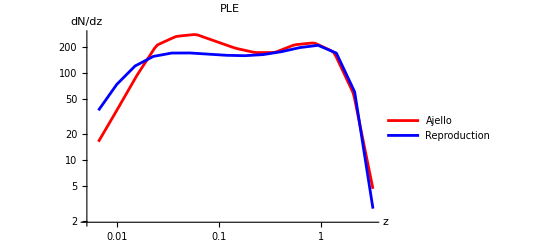

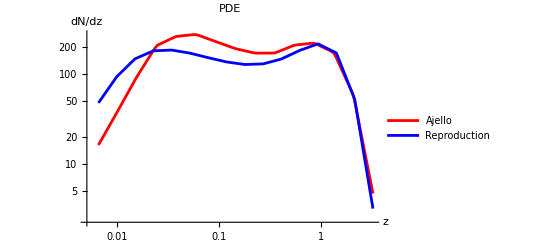

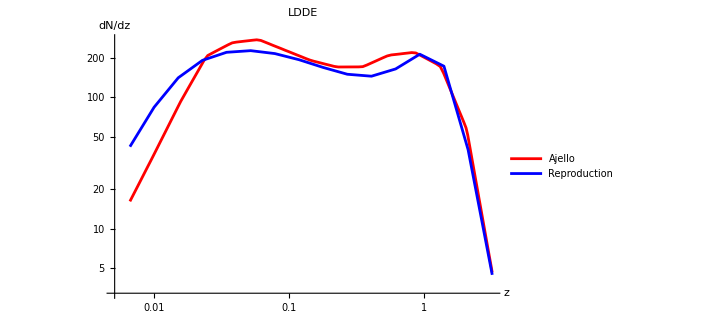

```mathematica
ListLogLogPlot[{dNdzAjello,Transpose[{dNdzPLEarrAjello[[All,1]],dNdzPLEarrAjello[[All,2]]/2}]},Joined->True,PlotStyle->{Red,Blue},PlotLabel->"PLE",AxesLabel->{"z","dN/dz"},PlotLegends->Placed[{ "Ajello","Reproduction"},{0.65,0.2}]]
ListLogLogPlot[{dNdzAjello,
Transpose[{dNdzPDEarrAjello[[All,1]],dNdzPDEarrAjello[[All,2]]/2}]},
Joined->True,PlotStyle->{Red,Blue},PlotLabel->"PDE",AxesLabel->{"z","dN/dz"},
PlotLegends->Placed[{ "Ajello","Reproduction"},{0.65,0.2}]]
ListLogLogPlot[{dNdzAjello,
Transpose[{dNdzLDDEarrAjello[[All,1]],dNdzLDDEarrAjello[[All,2]]/2}]},
Joined->True,PlotStyle->{Red,Blue},PlotLabel->"LDDE",AxesLabel->{"z","dN/dz"},
PlotLegends->Placed[{ "Ajello","Reproduction"},{0.65,0.2}]]
```

### dNdΓ

```mathematica
dNdΓPLEfuncAjello[Γ_]:=NIntegrate[Exp[L]*dVdz[z]*ΦPLEajello[Exp[L],Γ,z]*fermiSensitivityFuncAjello[fluxQu[Exp[L],Γ,z,0.1,100]],{z,10^-3,6},{L,Log[10^43],Log[10^52]},PrecisionGoal->5,Method->{Automatic,"SymbolicProcessing"->0}]//Quiet
dNdΓPDEfuncAjello[Γ_]:=NIntegrate[Exp[L]*dVdz[z]*ΦPDEajello[Exp[L],Γ,z]*fermiSensitivityFuncAjello[fluxQu[Exp[L],Γ,z,0.1,100]],{z,10^-3,6},{L,Log[10^43],Log[10^52]},PrecisionGoal->5,Method->{Automatic,"SymbolicProcessing"->0}]//Quiet
dNdΓLDDEfuncAjello[Γ_]:=NIntegrate[Exp[L]*dVdz[z]*ΦLDDEajello[Exp[L],Γ,z]*fermiSensitivityFuncAjello[fluxQu[Exp[L],Γ,z,0.1,100]],{z,10^-3,6},{L,Log[10^43],Log[10^52]},PrecisionGoal->5,Method->{Automatic,"SymbolicProcessing"->0}]//Quiet
```

```mathematica
Γarr=Range[1+.1,3,2/16];
dNdΓPLEarrAjello=ParallelTable[{Γ,dNdΓPLEfuncAjello[Γ]},{Γ,Γarr}];
CloseKernels[];
LaunchKernels[];
dNdΓPDEarrAjello=ParallelTable[{Γ,dNdΓPDEfuncAjello[Γ]},{Γ,Γarr}];
CloseKernels[];
LaunchKernels[];
dNdΓLDDEarrAjello=ParallelTable[{Γ,dNdΓLDDEfuncAjello[Γ]},{Γ,Γarr}];
CloseKernels[];
LaunchKernels[];
```

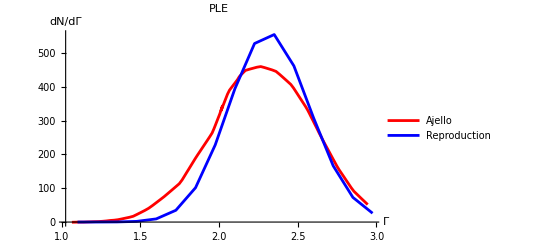

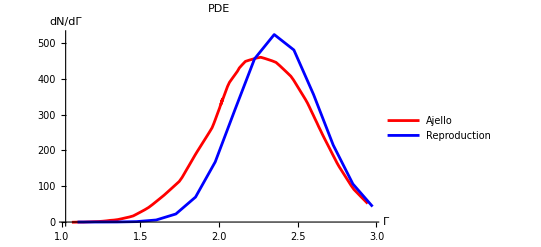

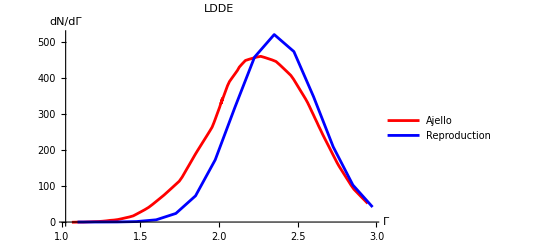

```mathematica
ListPlot[{dNdΓAjello,Transpose[{dNdΓPLEarrAjello[[All,1]],dNdΓPLEarrAjello[[All,2]]/2}]},Joined->True,PlotStyle->{Red,Blue},PlotLabel->"PLE",AxesLabel->{"Γ","dN/dΓ"},PlotLegends->Placed[{ "Ajello","Reproduction"},{0.65,0.2}]]
ListPlot[{dNdΓAjello,Transpose[{dNdΓPDEarrAjello[[All,1]],dNdΓPDEarrAjello[[All,2]]/2}]},Joined->True,PlotStyle->{Red,Blue},PlotLabel->"PDE",AxesLabel->{"Γ","dN/dΓ"},PlotLegends->Placed[{ "Ajello","Reproduction"},{0.65,0.2}]]
ListPlot[{dNdΓAjello,Transpose[{dNdΓLDDEarrAjello[[All,1]],dNdΓLDDEarrAjello[[All,2]]/2}]},Joined->True,PlotStyle->{Red,Blue},PlotLabel->"LDDE",AxesLabel->{"Γ","dN/dΓ"},PlotLegends->Placed[{ "Ajello","Reproduction"},{0.65,0.2}]]
```

```mathematica
fluxAjello[10^48,2.2,1,6000]
```

3.8572×10^-7

```mathematica
Expand[(x+I*p)/Sqrt[2]-(x-I*p)/Sqrt[2]]
```

ⅈ √2 p

```mathematica
Expand[(-I*Sqrt[(m*w*h)/2])^2]
```

-1/2 h m w